# VYA - Přednášky

## 1. Přednáška

### Tři důležité příkazy

```mathematica
Quiet[Remove["Global`*"]];
```

Vymaže předchozí definice

```mathematica
$HistoryLength = 2;
```

Omezuje paměť jádra, opatření proti přetečení paměti

```mathematica
SetDirectory[NotebookDirectory[]];
```

SetDir. ~ zavede místo nalezené NotebookDir. ~ cesta k lokaci. jako defaultní adresář

### Struktura výrazu, základy syntaxu

? ~ Help, fomát ? + symbol

```mathematica
?=
```

```mathematica
Vyraz = x+y + Sin[x^2+2*x*y+3]
```

x+y+Sin[3+x^2+2 x y]

```mathematica
Vyraz = x + y + Sin[x^2 + 2xy +3];
```

; ~ Input bez výstupu

```mathematica
?;
```

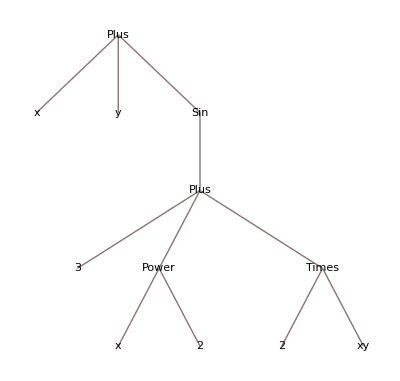

```mathematica
TreeForm[Vyraz]
```

```mathematica
?TreeForm
```

```mathematica
FullForm[Vyraz]
```

Plus[x,y,Sin[Plus[3,Power[x,2],Times[2,xy]]]]

```mathematica
Plus[x,y,Sin[Plus[3,Power[x,2],Times[2,xy]]]]
```

x+y+Sin[3+x^2+2 xy]

```mathematica
?FullForm
```

```mathematica
Head[Vyraz]
```

Plus

```mathematica
?Head
```

```mathematica
Attributes[Plus]
```

{Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}

```mathematica
?Attributes
```

### List

```mathematica
ListTree = {1, {2, 3}, {0,{ A, B}}}
```

{1,{2,3},{0,{A,B}}}

{1,{2,3},{0,{A,B}}}

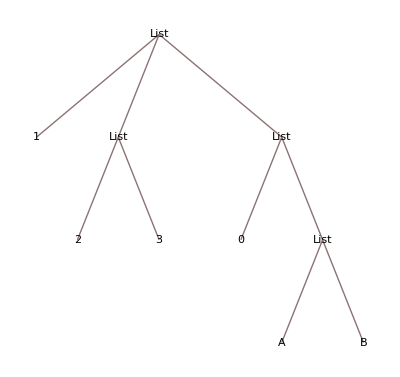

```mathematica
{1,{2,3},{0,{A,B}}}
TreeForm[ListTree]
```

```mathematica
ListTree[[1]]
ListTree[[2]]
ListTree[[3]]
ListTree[[-1]]
```

1

{2,3}

{0,{A,B}}

{0,{A,B}}

```mathematica
ListTree[[0]]
```

List

```mathematica
ListTree[[3, 2, 1]]
```

A

```mathematica
ListTree[[-1,-1,-1]]=C;
ListTree
```

{1,{2,3},{0,{A,C}}}

```mathematica
?Part
```

```mathematica
Length[ListTree]
```

3

```mathematica
?Length
```

```mathematica
Head[ListTree]
ListTree[[0]]
```

List

List

```mathematica
First[ListTree]
ListTree[[1]]
```

1

1

```mathematica
Last[ListTree]
ListTree[[-1]]
```

{0,{A,C}}

{0,{A,C}}

Volání výrazů

```mathematica
{Sin[x], Sin@x, x//Sin}
```

{Sin[x],Sin[x],Sin[x]}

### Souvislost listu a výrazu

```mathematica
TreeForm[Vyraz]
```

-Graphics-

```mathematica
Vyraz[[0]]
Head[Vyraz]
```

Plus

Plus

```mathematica
Vyraz[[1]]
First[Vyraz]
```

x

x

```mathematica
Vyraz[[2]]
Vyraz[[3]]
Vyraz[[-1]]
Last[Vyraz]
```

y

Sin[3+x^2+2 xy]

Sin[3+x^2+2 xy]

Sin[3+x^2+2 xy]

```mathematica
Vyraz[[3, 1]]
```

3+x^2+2 xy

```mathematica
Vyraz[[3, 1, 1]]
Vyraz[[3, 1, 2]]
Vyraz[[3, 1, 2, 1]]
Vyraz[[3, 1, 2, 2]]
Vyraz[[3, 1, 3]]
Vyraz[[3, 1, 3, 1]]
```

3

x^2

x

2

2 xy

2

### Pravidla a programování pomocí nich

```mathematica
x^2 /. x ->2
ReplaceAll[x^2,Rule[x,2]]
```

4

4

/.	=	ReplaceAll
→	=	Rule

```mathematica
?ReplaceAll
```

```mathematica
?Rule
```

```mathematica
x^2 + y /. {x-> E, y ->Pi}
```

ⅇ^2+π

```mathematica
x^2 + y /. {x-> E, y ->Pi, x->C}
```

ⅇ^2+π

```mathematica
1/(I*w*c) /. {c -> 10nF, nF -> 10^-9}
1/(I*w*c) /. {c -> 10nF}
```

-ⅈ/(10 nF w)

-ⅈ/(10 nF w)

```mathematica
1/(I*w*c) //. {c -> 10nF, nF -> 10^-9}
```

-(100000000 ⅈ)/w

//.	=	ReplaceRepeated

```mathematica
?ReplaceRepeated
```

```mathematica
(*x //. {x-> y+x, y -> x}*)
```

```mathematica
x^2 /. {{x -> 2}, {x -> 3}, {x -> 4}}
```

{4,9,16}

==	=	Equal

```mathematica
?Equal
```

```mathematica
Equal[lhs, rhs]
lhs == rhs
```

lhs==rhs

lhs==rhs

```mathematica
{1 == 1, 1 == 2, Equal[1,1], Equal[1,2]}
```

{True,False,True,False}

Pro řešení kořenů rovnice

```mathematica
Rovnice = x^3 + (2 + I)*x^2 + 2I*x + 14 == 0
```

14+2 ⅈ x+(2+ⅈ) x^2+x^3==0

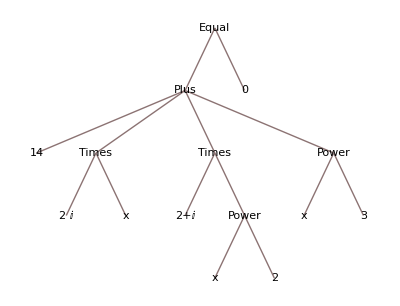

```mathematica
TreeForm[Rovnice]
```

```mathematica
lhs = Rovnice[[1]]
rhs = Rovnice[[2]]
```

14+2 ⅈ x+(2+ⅈ) x^2+x^3

0

```mathematica
Reseni = Solve[Rovnice]
```

{{x→Root-3.26-0.216 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,1}]-3.2597827730546176},{x→Root0.578+1.62 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,2}]0.5775176009540709},{x→Root0.682-2.40 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,3}]0.6822651721005469}}

{{x→Root-3.26-0.216 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,1}]-3.2597827730546176},{x→Root0.578+1.62 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,2}]0.5775176009540709},{x→Root0.682-2.40 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,3}]0.6822651721005469}}

```mathematica
Rovnice = x^3 + (2 + I)*x^2 + 2I*x + 14. == 0
```

14.+2 ⅈ x+(2+ⅈ) x^2+x^3==0

```mathematica
14.+2 ⅈ x+(2+ⅈ) x^2+x^3==0
Reseni = Solve[Rovnice]
x /. Solve[Rovnice]
```

14.+2 ⅈ x+(2+ⅈ) x^2+x^3==0

{{x→Root-3.26-0.216 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,1}]-3.2597827730546176},{x→Root0.578+1.62 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,2}]0.5775176009540709},{x→Root0.682-2.40 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,3}]0.6822651721005469}}

{Root-3.26-0.216 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,1}]-3.2597827730546176,Root0.578+1.62 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,2}]0.5775176009540709,Root0.682-2.40 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,3}]0.6822651721005469}

```mathematica
x1 = x /. Reseni[[1]]
x2 = x /. Reseni[[2]]
x3 = x /. Reseni[[3]]
```

Root-3.26-0.216 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,1}]-3.2597827730546176

Root0.578+1.62 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,2}]0.5775176009540709

Root0.682-2.40 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,3}]0.6822651721005469

```mathematica
Vysledek = x1 + 2*x2
```

Root-3.26-0.216 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,1}]-3.2597827730546176+2 Root0.578+1.62 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,2}]0.5775176009540709

```mathematica
FormVysledku = a + 2*b;
FormVysledku /. {a -> x1, b -> x2}
```

Root-3.26-0.216 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,1}]-3.2597827730546176+2 Root0.578+1.62 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,2}]0.5775176009540709

```mathematica
Print["x1 + 2*x2 = ", Vysledek]
(x /. Reseni) . {1, 2, 0}
```

x1 + 2*x2 = Root-3.26-0.216 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,1}]-3.2597827730546176+2 Root0.578+1.62 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,2}]0.5775176009540709

Root-3.26-0.216 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,1}]-3.2597827730546176+2 Root0.578+1.62 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,2}]0.5775176009540709

```mathematica
Expres = y - x /. {{x -> 2}, {x -> 3}, {x -> 4}}
Expres /. {List -> Times}
(Expres /. {List -> Times}) /. {y -> x}
Expand[(Expres /. {List -> Times}) /. {y -> x}]
0 == Expand[(Expres /. {List -> Times}) /. {y -> x}]
Reseni = Solve[0 == Expand[(Expres /. {List -> Times}) /. {y -> x}]]
```

{-2+y,-3+y,-4+y}

(-4+y) (-3+y) (-2+y)

(-4+x) (-3+x) (-2+x)

-24+26 x-9 x^2+x^3

0==-24+26 x-9 x^2+x^3

{{x→2},{x→3},{x→4}}

```mathematica
x1 = x /. Reseni[[1]];
x2 = x /. Reseni[[2]];
x3 = x /. Reseni[[3]];
Print["x1 = ", x1]
Print["x2 = ", x2]
Print["x3 = ", x3]
```

x1 = 2

x2 = 3

x3 = 4

```mathematica
Reseni[[1]]
Reseni[[1,1]]
Reseni[[1,1,1]]
Reseni[[1,1,2]]
xRes = {Reseni[[1,1,2]], Reseni[[2,1,2]], Reseni[[3,1,2]]}
```

{x→2}

x→2

x

2

{2,3,4}

```mathematica
Range[100]
Range[100] /. List -> Plus
Range[100] /. List -> Times
N[Range[100] /. List -> Times]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

5050

93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000

9.33262×10^157

### Patterny

```mathematica
?_
```

```mathematica
?__
```

```mathematica
?___
```

```mathematica
Vyraz = Sin[x^2 + 3] + x^y + E^Pi
```

ⅇ^π+x^y+Sin[3+x^2]

```mathematica
Vyraz /. a_^b_ -> b^a
Vyraz /. a_^b_ :> b^a
```

π^ⅇ+y^x+Sin[3+2^x]

π^ⅇ+y^x+Sin[3+2^x]

```mathematica
?:>
```

```mathematica
Vyraz /. {x^2 -> 2^x, x^y -> y^x}
Vyraz /. x^b_ :> b^x
```

ⅇ^π+y^x+Sin[3+2^x]

ⅇ^π+y^x+Sin[3+2^x]

## 2. Přednáška

```mathematica
Quiet@Remove["Global`*"];
```

### Rule a RuleDelay

```mathematica
Rule[a,b]
a -> b
```

a→b

a→b

```mathematica
RuleDelayed[a,b]
a :> b
```

a:>b

a:>b

:>	=	RuleDelayed

```mathematica
?RuleDelayed
```

```mathematica
Vyraz = Sin[x^2 + 3] + x^y + E^Pi
```

ⅇ^π+x^y+Sin[3+x^2]

```mathematica
a=5;
Vyraz /. a_^b_ :> b^a
Vyraz /. a_^b_ -> b^a
```

π^ⅇ+y^x+Sin[3+2^x]

π^5+y^5+Sin[35]

### Funkce

```mathematica
a = 6;
?a
```

```mathematica
f[x_] := x^2
f[x_,y_] := x^2 + y
```

```mathematica
?f
```

```mathematica
?:=
```

```mathematica
ClearAll[f]
f[x:_] := x^2
f[2]
```

4

```mathematica
ClearAll[f]
f[x_] := x^2
f[2]
?f
```

4

```mathematica
ClearAll[f];
f[x_] := 1+1
?f
```

```mathematica
f[x_] = 1+1
?f
```

2

```mathematica
Ran := Random[]
{Ran, Ran, Ran, Ran}
?Ran
```

{0.884187,0.822339,0.0181411,0.358902}

```mathematica
Ran = Random[]
{Ran, Ran, Ran, Ran}
?Ran
```

0.202024

{0.202024,0.202024,0.202024,0.202024}

```mathematica
ClearAll[f]
x = 5;
f[x_] := x^2
f[2]
f[5]
f[x]
?f
```

4

25

25

```mathematica
ClearAll[f]
x = 5;
f[x_] = x^2
f[2]
f[5]
f[x]
?f
```

25

25

25

«1 more identical outputs»

```mathematica
ClearAll[f, x]
f[x_] = x^2
f[2]
f[5]
f[x]
?f
```

x^2

4

25

x^2

```mathematica
ClearAll[f]
f[x_] := FindRoot[Cos[a*x] == a, {a, 0}]
f[0.5]
```

{6→0.900367}

```mathematica
?FindRoot
```

```mathematica
ClearAll[f,a]
f[x_] = FindRoot[Cos[a*x] == a, {a, 0}]
f[0.5]
```

FindRoot::nlnum: The function value {-1.+Cos[1. x]} is not a list of numbers with dimensions {1} at {a} = {1.}.

{a→0.}

{a→0.}

```mathematica
ClearAll[f]
f[x_] = Integrate[x^0.5 * Sin[x],x]
f[0.1]
```

-(0.5 x^0.5 Gamma[1.5,(0.-1. ⅈ) x])/((0.-1. ⅈ) x)^0.5-(0.5 x^0.5 Gamma[1.5,(0.+1. ⅈ) x])/((0.+1. ⅈ) x)^0.5

-0.625393+0. ⅈ

### Set a SetDelay

www.mathworld.com

```mathematica
ClearAll[f]
f[x_] := Integrate[x^0.5 * Sin[x], x]
f[0.1]
```

Integrate::ilim: Invalid integration variable or limit(s) in 0.1.

∫0.0315701ⅆ0.1

```mathematica
ClearAll[f]
f[x_] := x^2
f[0] := 100
f[x_Integer] := 1/x
{f[3], f[3.], f[0], f[3]}
```

{1/3,9.,100,1/3}

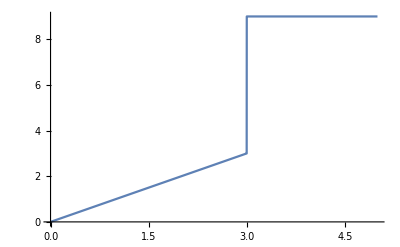

```mathematica
ClearAll[f, Test]
Test[y_] := y <= 3
f[x_?Test] := x
f[x_] := 9
Plot[f[x], {x, 0, 5}]
```

```mathematica
ClearAll[a]
a[n_] := n*a[n-1]
a[0] := 1
a[3]
Trace[a[3]]
```

6

{a[3],3 a[3-1],{{3-1,2},a[2],2 a[2-1],{{2-1,1},a[1],1 a[1-1],{{1-1,0},a[0],1},1 1,1},2 1,2},3 2,6}

```mathematica
?Trace
```

#### Table

```mathematica
Table[predmet, {10}]
```

{predmet,predmet,predmet,predmet,predmet,predmet,predmet,predmet,predmet,predmet}

```mathematica
?Table
```

```mathematica
Table[x^2, {x,10}]
Table[x^2, {x, 2, 10}]
Table[x^2, {x, 3, 10, 0.2}]
```

{1,4,9,16,25,36,49,64,81,100}

{4,9,16,25,36,49,64,81,100}

{9.,10.24,11.56,12.96,14.44,16.,17.64,19.36,21.16,23.04,25.,27.04,29.16,31.36,33.64,36.,38.44,40.96,43.56,46.24,49.,51.84,54.76,57.76,60.84,64.,67.24,70.56,73.96,77.44,81.,84.64,88.36,92.16,96.04,100.}

```mathematica
ClearAll[a, n, i]
a[n_Integer] := n*a[n-1]
a[0] := 1
Table[a[i], {i, 100}];
Timing[Table[a[i], {i,100}]][[1]]
```

0.015625

```mathematica
?Timing
```

Timing[[1]]	=	Čas potřebný pro výpočet

```mathematica
?$RecursionLimit
```

```mathematica
$RecursionLimit = 10^5;
ClearAll[a, n]
a[n_Integer] := a[n] = n*a[n-1]
a[0] := 1
a[6]
Trace[a[7]]
?a
(*Timing[Table[a[i], {i, 3000}]][[1]]*)
```

720

{a[7],a[7]=7 a[7-1],{{{7-1,6},a[6],720},7 720,5040},a[7]=5040,5040}

### Funkce podmíněně definovaná

```mathematica
Quiet@Remove["Global`*"];
?/;
```

```mathematica
ClearAll[f]
f[x_] := x /; x <= 3
```

```mathematica
f[x_] := 9 /; x > 3
Plot[f[x], {x, 0, 5}]
```

-Graphics-

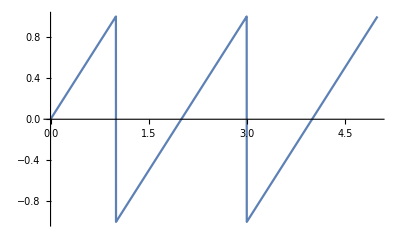

```mathematica
ClearAll[f]
f[x_] := x /; x<= 1
f[x_] := f[x-2] /; x > 1
f[x_] := f[x+2] /; x <= -1
Plot[f[x], {x, 0, 5}]
```

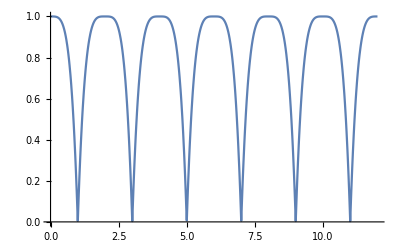

```mathematica
ClearAll[f]
f[x_] := 1 - x^4 /; -1 < x<= 1
f[x_] := f[x-2] /; x > 1
f[x_] := f[x+2] /; x <= -1
Plot[f[x], {x, 0, 12 }]
```

```mathematica
Trace[f[-5.5]]
```

{f[-5.5],{{-1<-5.5≤1,False},RuleCondition[$ConditionHold[$ConditionHold[1-(-5.5)^4]],False],Fail},{{-5.5>1,False},RuleCondition[$ConditionHold[$ConditionHold[f[-5.5-2]]],False],Fail},{{-5.5≤-1,True},RuleCondition[$ConditionHold[$ConditionHold[f[-5.5+2]]],True],$ConditionHold[$ConditionHold[f[-5.5+2]]]},f[-5.5+2],{-5.5+2,-3.5},f[-3.5],{{-1<-3.5≤1,False},RuleCondition[$ConditionHold[$ConditionHold[1-(-3.5)^4]],False],Fail},{{-3.5>1,False},RuleCondition[$ConditionHold[$ConditionHold[f[-3.5-2]]],False],Fail},{{-3.5≤-1,True},RuleCondition[$ConditionHold[$ConditionHold[f[-3.5+2]]],True],$ConditionHold[$ConditionHold[f[-3.5+2]]]},f[-3.5+2],{-3.5+2,-1.5},f[-1.5],{{-1<-1.5≤1,False},RuleCondition[$ConditionHold[$ConditionHold[1-(-1.5)^4]],False],Fail},{{-1.5>1,False},RuleCondition[$ConditionHold[$ConditionHold[f[-1.5-2]]],False],Fail},{{-1.5≤-1,True},RuleCondition[$ConditionHold[$ConditionHold[f[-1.5+2]]],True],$ConditionHold[$ConditionHold[f[-1.5+2]]]},f[-1.5+2],{-1.5+2,0.5},f[0.5],{{-1<0.5≤1,True},RuleCondition[$ConditionHold[$ConditionHold[1-0.5^4]],True],$ConditionHold[$ConditionHold[1-0.5^4]]},1-0.5^4,{{0.5^4,0.0625},-0.0625,-0.0625},1-0.0625,0.9375}

```mathematica
?Which
```

```mathematica
?Piecewise
```

### Formáty parametrů

```mathematica
ClearAll[a]
a[{x_, y_}] := x + y
a[{Pi, 2E}]
```

2 ⅇ+π

### Úkol 2

l---o^vp----------i^vc-->   o-pavouk, i-člověk
Diferenciální rovnice
Člověk utíká od stěny s níž je spojený leteckou gumou, utíká před pavoukem který leze po gumě směrem k němu
vc - rychlost člověka, vůči absolutnímu prostoru
vp - rychlost pavouka,  vůči gumě

## 3. Přednáška

### Používání AI

https://chat.openai.com/

Zadání: “Prosím, napiš skript ve Wolfram Mathematica, který vygeneruje graf funkcí Sin a Cos, sinus modře a kosínus červeně, popíše osy a graf bude mít GridLines”

Odpoveď: “Samozřejmě, zde je skript ve Wolfram Mathematica, který vygeneruje graf funkcí Sin a Cos s popisem os a s GridLines:”

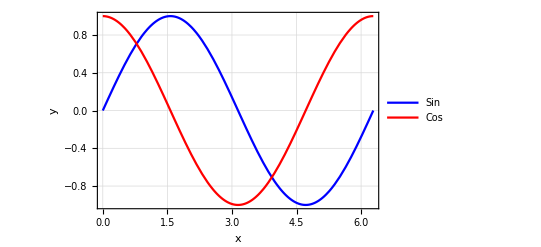

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2 Pi},PlotStyle->{Blue,Red},Frame->True,FrameLabel->{Style["x",Bold,14],Style["y",Bold,14]},PlotLegends->{"Sin","Cos"},GridLines->Automatic,GridLinesStyle->LightGray,ImageSize->400]
```

“Tento skript vykreslí graf funkcí Sin a Cos na intervalu [0, 2 Pi]. Sinus je vykreslen modře a kosinus červeně. Osa x je popsaná nápisem “x” a osa y nápisem “y”. Graf má také mřížky (GridLines) s šedým stylem (GridLinesStyle). Celková velikost grafu je nastavena na 400 pixelů.

Můžete tento skript spustit ve Wolfram Mathematica a zobrazí se vám výsledný graf.”

### Příkaz module

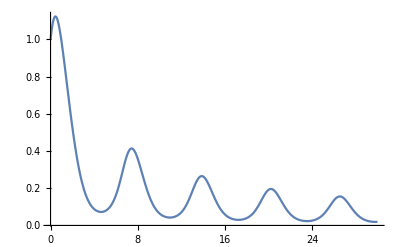

```mathematica
Quiet@Remove["Global`*"];
s[a_] := NDSolve[{y'[x] == y[x] Cos[x + a*y[x]], y[0] == 1}, y, {x, 0, 30}]
g[a_] := Plot[Evaluate[y[x] /. s[a]], {x, 0, 30}, PlotRange -> All]
g[1]
```

```mathematica
Quiet@Remove["Global`*"];
f[a_] := Module[{reseni}, reseni = NDSolve[{y'[x] == y[x]Cos[x + a*y[x]], y[0] == 1}, y, {x, 0, 30}];
	Plot[Evaluate[y[x] /. s[a]], {x, 0, 30}, PlotRange -> All]]
f[2]
```

1

### Užitečná funkce Tanh

5/2+1/2 Tanh[5 (-4+x)]

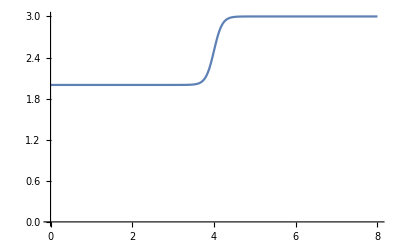

```mathematica
Quiet@Remove["Global`*"];
Prechod[Odkud_, Kam_, Zmena_, Strmost_, Promenna_] := Module[{Rovnice, a, b, Dosaz}, 
Rovnice = {a - b == Odkud, a + b == Kam};
Dosaz = Solve[Rovnice, {a, b}][[1]]; 
a+b*Tanh[Strmost*(Promenna - Zmena)] /. Dosaz];
Graf = Prechod[2, 3, 4, 5, x]
Plot[Graf, {x, 0, 8}, AxesOrigin -> {0, 0}]
```

### Pure functions

```mathematica
Quiet@Remove["Global`*"];
f[x_] := x^2;
f[5]
```

25

```mathematica
?#
```

```mathematica
#^2 & [5]
```

25

```mathematica
g[x_,y_] := x + y^2
g[E, Pi]
```

ⅇ+π^2

```mathematica
#1 + #2^2 & [E, Pi]
```

ⅇ+π^2

```mathematica
h := #1 + #2^2&
h[E, Pi]
```

ⅇ+π^2

```mathematica
?Select
```

```mathematica
Test[x_] := x > 2
Test[1]
Test[3]
Select[{1, 2, 4, 3, 7, 6, 5, 8}, Test]
```

False

True

{4,3,7,6,5,8}

```mathematica
Select[{1, 2, 4, 3, 7, 6, 5, 8}, # > 2 &]
```

{4,3,7,6,5,8}

```mathematica
# > 2 & [1]
```

False

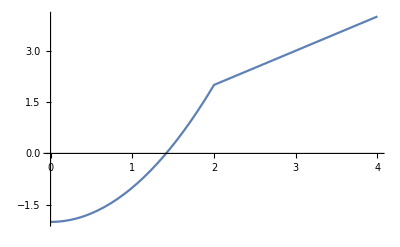

```mathematica
Quiet@Remove["Global`*"];
Test[x_] := x > 2
f[x_?Test] := x
f[x_] := x^2-2
Plot[f[x], {x, 0, 4}]
```

```mathematica
Quiet@Remove["Global`*"];
```

```mathematica
f[x_? (# > 2 &)] := x
f[x_] := x^2-2
Plot[f[x], {x, 0, 4}]
```

-Graphics-

### Map a Apply

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
?Map
```

```mathematica
Map[f, {1, 2, 3, 4}]
f /@ {1, 2, 3, 4}
```

{f[1],f[2],f[3],f[4]}

{f[1],f[2],f[3],f[4]}

```mathematica
Sin[{1, 2, 3, 4}]
```

{Sin[1],Sin[2],Sin[3],Sin[4]}

```mathematica
Sin /@ {1, 2, 3, 4}
```

{Sin[1],Sin[2],Sin[3],Sin[4]}

```mathematica
Attributes[Sin]
```

{Listable,NumericFunction,Protected}

```mathematica
Quiet[Remove["Global`*"]];
?Apply
```

```mathematica
Apply[f, {1, 2, 3, 4}]
f @@ {1, 2, 3, 4}
```

f[1,2,3,4]

f[1,2,3,4]

```mathematica
Apply[f, Map[f, {1, 2, 3, 4}]]
f @@ (f /@ {1, 2, 3, 4})
```

f[f[1],f[2],f[3],f[4]]

f[f[1],f[2],f[3],f[4]]

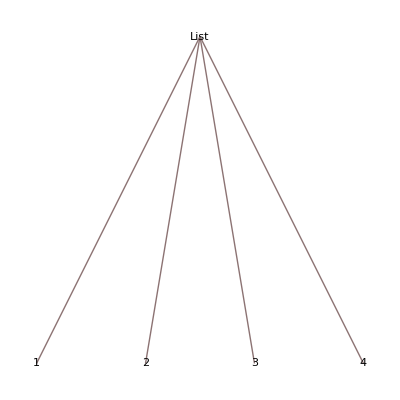
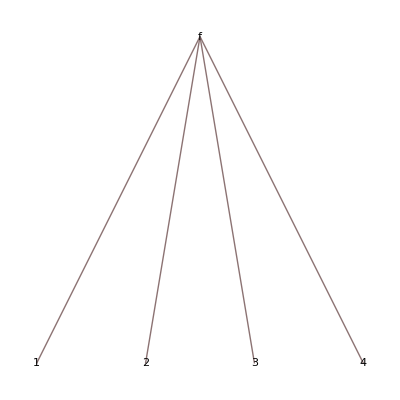

```mathematica
{TreeForm[{1, 2, 3, 4}], TreeForm[f @@ {1, 2, 3, 4}]}
```

{{-1,0,2},{5,2,0},{5,-5,0}}

(-1 | 0 | 2
5 | 2 | 0
5 | -5 | 0)

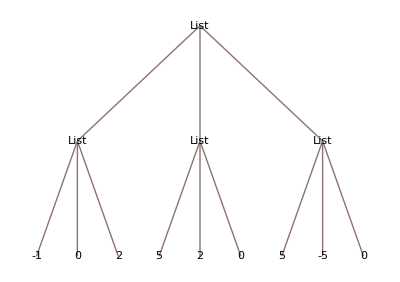

```mathematica
Matice = Table[RandomInteger[{-5,5}], {i,3}, {j,3}]
MatrixForm[Matice]
TreeForm[Matice]
```

```mathematica
Matice /. List -> Plus
```

8

```mathematica
f @@ Matice
Plus @@ Matice
```

f[{-1,0,2},{5,2,0},{5,-5,0}]

{9,-3,2}

```mathematica
f[x_] := x^3
f[Range[10]]
#^3 & /@ Range[10]
```

{1,8,27,64,125,216,343,512,729,1000}

```mathematica
{1,8,27,64,125,216,343,512,729,1000}
```

```mathematica
Plus @@ (#^3 & /@ Range[10])
```

```mathematica
Plus @@ (#^3 & /@ Range[10])
∑_(i=1)^10 i^3
```

3025

3025


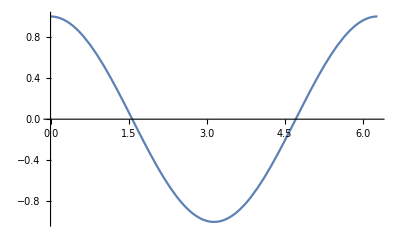
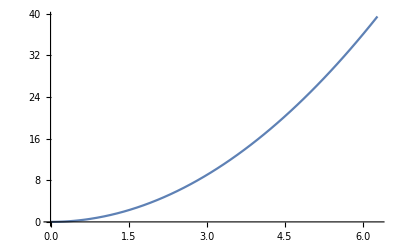

```mathematica
Plot[#[x], {x, 0, 2Pi}] & /@ {Sin, Cos, #^2 &}
```

### NumberQ a NumericQ

```mathematica
?NumberQ
```

```mathematica
?NumericQ
```

```mathematica
NumberQ[Pi]
```

False

```mathematica
NumericQ[Pi]
```

True

```mathematica
?N
```

```mathematica
Pi + 2E
```

2 ⅇ+π

```mathematica
N[Pi + 2E]
```

8.57816d

```mathematica
N[Pi, #] & /@ Range[5, 20, 1]
```

{3.1416,3.14159,3.141593,3.1415927,3.14159265,3.141592654,3.1415926536,3.14159265359,3.14159265359,3.1415926535898,3.14159265358979,3.141592653589793,3.1415926535897932,3.14159265358979324,3.141592653589793238,3.1415926535897932385}

### Eulerova metoda

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
Derivace[{t_, y_}] := -2y;
PocBod = {t0, y0} = {0, 10};
tMax = 2;
nKroku = 10;
Δt = (tMax - t0)/nKroku
KrokEuler[Bod:{t_, y_}] := {t + Δt, y + Δt * Derivace[Bod]}
KrokEuler[PocBod]
```

1/5

{1/5,6}

### Nest

```mathematica
?Nest
```

```mathematica
Nest[f, x, 5]
```

f[f[f[f[f[x]]]]]

```mathematica
?NestList
```

```mathematica
NestList[f, x, 5]
```

{x,f[x],f[f[x]],f[f[f[x]]],f[f[f[f[x]]]],f[f[f[f[f[x]]]]]}

```mathematica
KrokEuler[Bod:{t_, y_}] := {t + Δt, y + Δt * Derivace[Bod]}
Reseni = NestList[KrokEuler, PocBod, nKroku]
```

{{0,10},{1/5,6},{2/5,18/5},{3/5,54/25},{4/5,162/125},{1,486/625},{6/5,1458/3125},{7/5,4374/15625},{8/5,13122/78125},{9/5,39366/390625},{2,118098/1953125}}

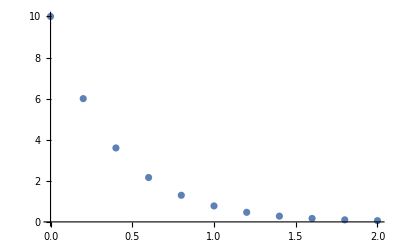

```mathematica
ListPlot[Reseni]
```

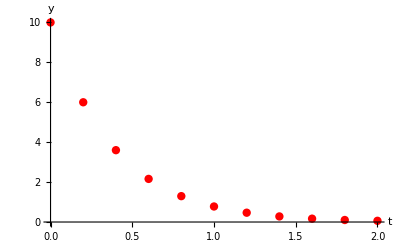

```mathematica
ListPlot[Reseni, AxesLabel->{"t", "y"}, PlotStyle->{PointSize[0.015], Red}, GridLines->Full]
```

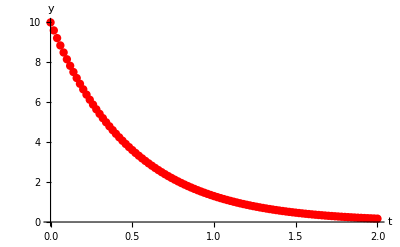

```mathematica
Derivace[{t_, y_}] := -2y;
PocBod = {t0, y0} = {0, 10};
tMax = 2;
nKroku = 100;
Δt = (tMax - t0)/nKroku;
KrokEuler[Bod:{t_, y_}] := {t + Δt, y + Δt * Derivace[Bod]}
Reseni = NestList[KrokEuler, PocBod, nKroku];
ListPlot[Reseni, AxesLabel->{"t", "y"}, PlotStyle->{PointSize[0.015], Red}, GridLines->Full]
```

### NDSolve

```mathematica
?NDSolve
```

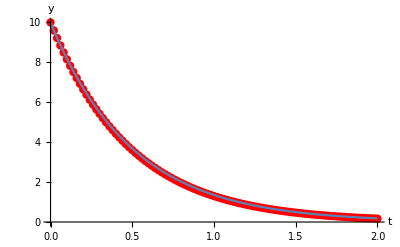

```mathematica
PltEuler = ListPlot[Reseni, AxesLabel->{"t", "y"}, PlotStyle->{PointSize[0.015], Red}, GridLines->Full];

RvncNDSolve = {y'[t] == Derivace[{t, y[t]}], y[t0] == y0};
SlvNDS = NDSolve[RvncNDSolve, y, {t, t0, tMax}][[1]];
PltNDS = Plot[y[t] /. SlvNDS, {t, t0, tMax}];
Show[PltEuler, PltNDS]
```

## 4. Přednáška

### Úvod - Numerická integrace

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
Vrz[x_] := a*x^2 + b*x + c;
Rvnc = {Vrz[x0] == f0, Vrz[x0  + Δx] == fPlus, Vrz[x0 - Δx] == fMinus}
```

{c+b x0+a x0^2==f0,c+b (x0+Δx)+a (x0+Δx)^2==fPlus,c+b (x0-Δx)+a (x0-Δx)^2==fMinus}

```mathematica
Solve[Rvnc, {a, b, c}];
DszABC = Solve[Rvnc, {a, b, c}][[1]];
Integrand = Vrz[x] /. DszABC
Integral = Integrate[Integrand, {x, x0 - Δx, x0 + Δx}] //Simplify
```

-((2 f0-fMinus-fPlus) x^2)/(2 Δx^2)-1/(2 Δx^2)x (-4 f0 x0+2 fMinus x0+2 fPlus x0+fMinus Δx-fPlus Δx)-1/(2 Δx^2)(2 f0 x0^2-fMinus x0^2-fPlus x0^2-fMinus x0 Δx+fPlus x0 Δx-2 f0 Δx^2)

1/3 (4 f0+fMinus+fPlus) Δx

### Simpsonova metoda

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
?OddQ
```

```mathematica
{OddQ[3], OddQ[4], EvenQ[4]}
```

{True,False,True}

```mathematica
list = Subscript[a, #] & /@ Range[9]
Trojice = Partition[list, 3, 2]
```

{a_1,a_2,a_3,a_4,a_5,a_6,a_7,a_8,a_9}

{{a_1,a_2,a_3},{a_3,a_4,a_5},{a_5,a_6,a_7},{a_7,a_8,a_9}}

```mathematica
Trojice // Length
```

4

```mathematica
list = Subscript[a, #] & /@ Range[9];
Trojice = Partition[list, 3, 2];

Trojice /. {a_, b_, c_} :> a + 4b + c 
Vydej[{a_, b_, c_}] := a + 4b +c;
Vydej /@ Trojice
{1, 4, 1}.# & /@ Trojice
```

{a_1+4 a_2+a_3,a_3+4 a_4+a_5,a_5+4 a_6+a_7,a_7+4 a_8+a_9}

{a_1+4 a_2+a_3,a_3+4 a_4+a_5,a_5+4 a_6+a_7,a_7+4 a_8+a_9}

{a_1+4 a_2+a_3,a_3+4 a_4+a_5,a_5+4 a_6+a_7,a_7+4 a_8+a_9}

```mathematica
?Partition
```

```mathematica
Flatten[Partition[list, 3, 2]]
?Flatten
```

{a_1,a_2,a_3,a_3,a_4,a_5,a_5,a_6,a_7,a_7,a_8,a_9}

```mathematica
?Module
```

```mathematica
Quiet[Remove["Global`*"]];
Simpson[f_, xMin_, xMax_, nBodu_ ?OddQ] := Module[{xka, Δx, yka, trojka, vydej}, 
Δx = (xMax - xMin)/(nBodu - 1);
xka = Range[xMin, xMax, Δx] ;
yka = f /@ xka;
trojka = Partition[yka, 3, 2];
vydej[{a_, b_, c_}] := a + 4b +c;
Δx/3 Total[vydej /@ trojka]
];
Simpson[Sin, 0, Pi, 9]
N[Simpson[Sin, 0, Pi, 9]]
```

1/24 π (2+2 √2+8 Cos[π/8]+8 Sin[π/8])

2.00027

-2/3+4 √6+Log[6]+Sin[5]

9.96413

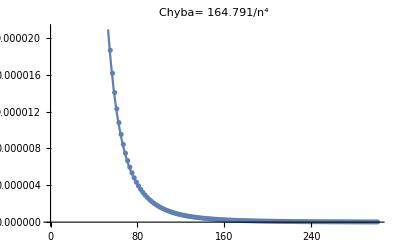

```mathematica
f[x_] := 1/(x+1) + √(x + 1) + Cos[x];
xMin = 0;
xMax = 5;
IntegralPres = Integrate[f[x], {x, xMin, xMax}]
N[IntegralPres]
Chyba[nBodu_ ?OddQ] :=Abs[ (Simpson[f, xMin, xMax, nBodu] - IntegralPres)/IntegralPres] * 100;

{nBMin, nBMax} = {17, 301};
DataChyb = Table[{nBodu, Chyba[nBodu]}, {nBodu, nBMin, nBMax, 2}];
Plt1 = ListPlot[DataChyb];
Proklad = Fit[DataChyb, {1/n^4}, n];
PltProklad = Plot[Proklad, {n, nBMin, nBMax}];
Show[Plt1, PltProklad, PlotLabel -> "Chyba= " <>ToString[TraditionalForm[Proklad]]]
```

### Úkol 4

https://youtu.be/63ocOSAF1gI?si=WfSZFMYCMfjLoHZ8&t=3153
Naprogramuj funkci, ktera si vezme n_Integer a odvodi vztah pro numerický integral
n = 1 je lichobežníková metoda
n = 2 je Simpsonova metoda
atd..

### Fit a Metoda nejmenší

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
?Fit
```

3.98461-4.00422 x+1.00374 x^2

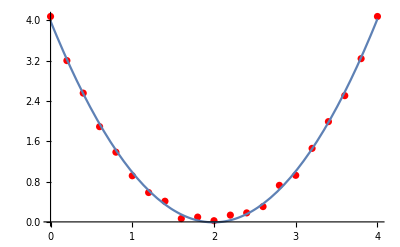

```mathematica
Data = {#, (# - 2)^2 + RandomReal[{-0.1, 0.1}]} & /@ Range[0, 4, 0.2];
Proklad = Fit[Data, {1, x, x^2}, x]
pltBody = ListPlot[Data, PlotStyle->Red];
pltProklad = Plot[Proklad, {x, 0, 4}];
Show[pltBody, pltProklad]
```

### RLC a Elektrické Obvody

Ohmův zákon - U = I * R
Elek. napětí - U [Volt] = Rozdíl potenciálů mezi dvěma body
Elek. proud - I [Amper] = Pohyb elek. za čas
Elek. odpor - R [Ohm]  = Vlastnost materiálu bránící průchodu elek. proudu

## 5. Přednáška

### Obvody a uzlová napětí

Rovnice součástek

1) Najdi uzly a zvol referenční 
2) Označ proudy
3) ZZ Proudu : 0 = I_1 + I_2 + I_3 +...
4) Rovnice součástek

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
R = 100;
μF = 10^-6;
mH = 0.001;
Cl = 4.7 μF;
L = 33mH;
Uz = 10*Tanh[5*Sin[314t]];
Iz = 0.01*Sin[√2 * 314t];
```

```mathematica
Rovn = {0 == IC[t] + IR[t] + IUz[t],
IUz[t] + Iz == IL[t],
U1[t] == R * IR[t],
IC[t] == Cl * U1'[t],
U2[t] == L * IL'[t],
Uz == U1[t] - U2[t] }
```

{0==IC[t]+IR[t]+IUz[t],IUz[t]+0.01 Sin[314 √2 t]==IL[t],U1[t]==100 IR[t],IC[t]==4.7×10^-6 U1'[t],U2[t]==0.033 IL'[t],10 Tanh[5 Sin[314 t]]==U1[t]-U2[t]}

### Cases

```mathematica
?Cases
```

```mathematica
Cases[Rovn, _[t], {0, ∞}]
```

{IC[t],IL[t],IUz[t],IUz[t],IL[t],U1[t],IR[t],IC[t],U1'[t],U2[t],IL'[t],U1[t],U2[t]}

```mathematica
?Union
```

```mathematica
Union[Cases[Rovn, _[t], {0, ∞}]]
```

{IC[t],IL[t],IR[t],IUz[t],U1[t],U2[t],IL'[t],U1'[t]}

```mathematica
FullForm[IL'[t]]
```

Derivative[1][IL][t]

```mathematica
Nezname = Union[Cases[Rovn, a_Symbol[t] :> a, {0, ∞}]]
```

{IC,IL,IR,IUz,U1,U2}

```mathematica
Length /@ {Rovn, Nezname}
PocPod = Union[Cases[Rovn, a_'[t] :> a[0] == 0, {0, ∞}]]
```

{6,6}

{IL[0]==0,U1[0]==0}

```mathematica
RovnPod = Union[Rovn, PocPod]
```

{0==IC[t]+IR[t]+IUz[t],IC[t]==4.7×10^-6 U1'[t],IL[0]==0,IUz[t]+0.01 Sin[314 √2 t]==IL[t],10 Tanh[5 Sin[314 t]]==U1[t]-U2[t],U1[0]==0,U1[t]==100 IR[t],U2[t]==0.033 IL'[t]}

```mathematica
tMax = 0.08;
Res = NDSolve[RovnPod, Nezname, {t, 0, tMax}, StartingStepSize->10^-9][[1]]
```

{IC→InterpolatingFunction[…],IL→InterpolatingFunction[…],IR→InterpolatingFunction[…],IUz→InterpolatingFunction[…],U1→InterpolatingFunction[…],U2→InterpolatingFunction[…]}

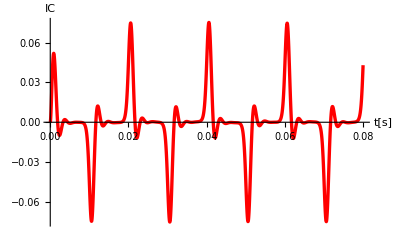
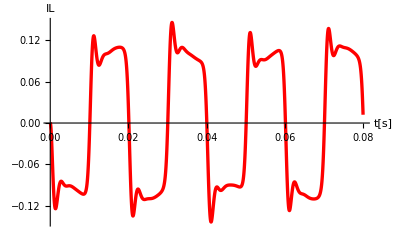
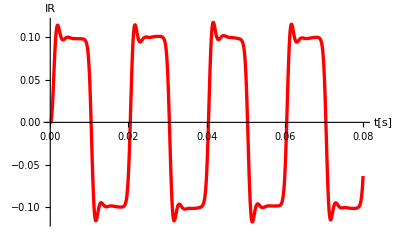
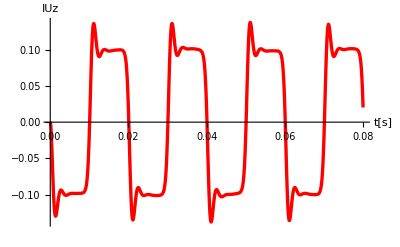
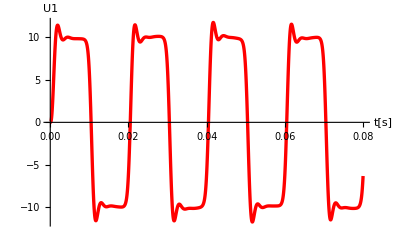
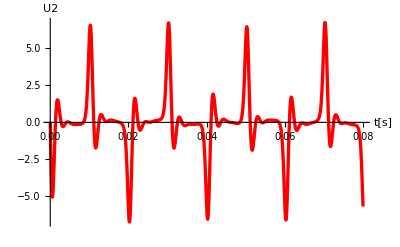

```mathematica
Plot[#[t] /. Res, {t, 0, tMax}, AxesLabel->{"t[s]", ToString[#]}, PlotRange->All, GridLines->Full, PlotStyle->{Red, Thickness[0.006]}] & /@ Nezname
```

```mathematica
Options[NDSolve]
```

{AccuracyGoal→Automatic,Compiled→Automatic,DependentVariables→Automatic,DiscreteVariables→{},EvaluationMonitor→None,InitialSeeding→{},InterpolationOrder→Automatic,MaxStepFraction→1/10,MaxSteps→Automatic,MaxStepSize→Automatic,Method→Automatic,NormFunction→Automatic,PrecisionGoal→Automatic,StartingStepSize→Automatic,StepMonitor→None,WorkingPrecision→MachinePrecision}

### Výkres pomocí Map a funkce obvodu

```mathematica
Quiet[Remove["Global`*"]];
```

{0==iC[t]+iR[t]+iUz[t],iUz[t]+0.01 Sin[314 √2 t]==iL[t],u1[t]==100 iR[t],iC[t]==4.7×10^-6 u1'[t],u2[t]==0.033 iL'[t],10 Tanh[5 Sin[314 t]]==u1[t]-u2[t]}

{iC,iL,iR,iUz,u1,u2}

{6,6}

{iL[0]==0,u1[0]==0}

{0==iC[t]+iR[t]+iUz[t],iC[t]==4.7×10^-6 u1'[t],iL[0]==0,iUz[t]+0.01 Sin[314 √2 t]==iL[t],10 Tanh[5 Sin[314 t]]==u1[t]-u2[t],u1[0]==0,u1[t]==100 iR[t],u2[t]==0.033 iL'[t]}

{iC→InterpolatingFunction[…],iL→InterpolatingFunction[…],iR→InterpolatingFunction[…],iUz→InterpolatingFunction[…],u1→InterpolatingFunction[…],u2→InterpolatingFunction[…]}

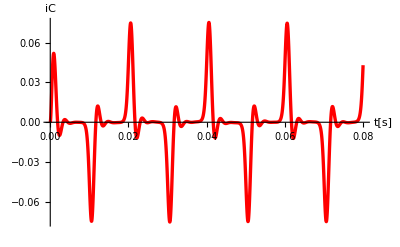
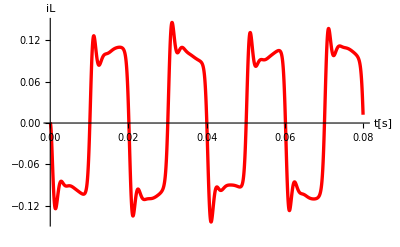
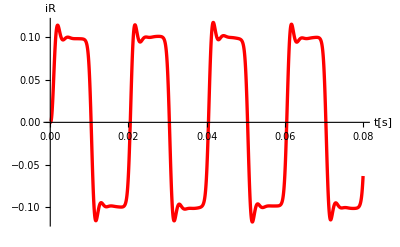
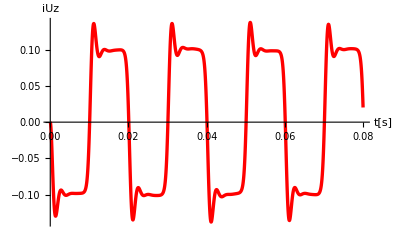
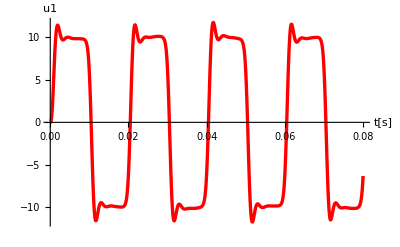
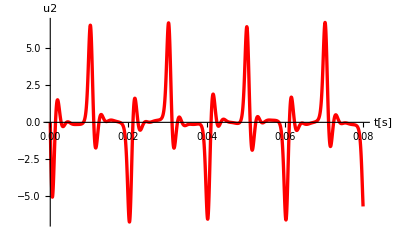

```mathematica
R = 100;
μF = 10^-6;
mH = 0.001;
c = 4.7 μF;
L = 33mH;
uz = 10*Tanh[5*Sin[314t]];
iz = 0.01*Sin[√2 * 314t];
rce = {0 == iC[t] + iR[t] + iUz[t],
iUz[t] + iz == iL[t],
u1[t] == R * iR[t],
iC[t] == c * u1'[t],
u2[t] == L *  iL'[t],
uz == u1[t] - u2[t]
}
nezname = Union[Cases[rce, a_Symbol[t] :> a, {0, ∞}]]
Length /@ {rce, nezname}
pocPodminky = Union[Cases[rce, a_'[t] :> a[0]== 0, {0, ∞}]]
rceDohromady = Union[rce, pocPodminky]
tmax = 0.08;
sol = NDSolve[rceDohromady, nezname, {t, 0, tmax}, StartingStepSize->10^-9][[1]]
Plot[#[t] /. sol, {t, 0, tmax}, AxesLabel->{"t[s]", ToString[#]}, PlotRange->All, GridLines->Full, PlotStyle->{Red, Thickness[0.006]}] & /@ nezname
```

### Jednocestný usměrňovač

```mathematica
Quiet[Remove["Global`*"]];
```

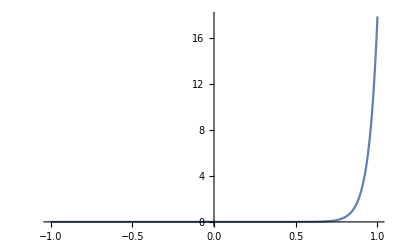

```mathematica
iD[uD_] := 10^-7 * (Exp[19uD] - 1)
Plot[iD[uD], {uD, -1, 1}, PlotRange->All]
```

```mathematica
Uz = 10 * √2*Sin[314t]
μF = 10^-6;
Cl = 470 μF;
R = 100;
```

10 √2 Sin[314 t]

```mathematica
Rovn = {Id[t] == IR[t] + IC[t],
0 == Id[t] + IUz[t],
U1[t] == R * IR[t],
IC[t] == Cl * U1'[t],
Id[t] == iD[U2[t] - U1[t]],
Uz == U2[t]
}
```

{Id[t]==IC[t]+IR[t],0==Id[t]+IUz[t],U1[t]==100 IR[t],IC[t]==(47 U1'[t])/100000,Id[t]==(-1+ⅇ^(19 (-U1[t]+U2[t])))/10000000,10 √2 Sin[314 t]==U2[t]}

```mathematica
Nezname = Union[Cases[Rovn, a_Symbol[t] :> a, {0, ∞}]]
Length /@ {Rovn, Nezname}
PocPod = Union[Cases[Rovn, a_'[t] :> a[0] == 0, {0, ∞}]]
```

{IC,Id,IR,IUz,U1,U2}

{6,6}

{U1[0]==0}

```mathematica
RovnPod = Union[Rovn, PocPod]
tMax = 0.08;
Res = NDSolve[RovnPod, Nezname, {t, 0, tMax}, StartingStepSize->10^-9][[1]]
```

{0==Id[t]+IUz[t],IC[t]==(47 U1'[t])/100000,Id[t]==(-1+ⅇ^(19 (-U1[t]+U2[t])))/10000000,Id[t]==IC[t]+IR[t],10 √2 Sin[314 t]==U2[t],U1[0]==0,U1[t]==100 IR[t]}

{IC→InterpolatingFunction[{{0., 0.08}}, <>],Id→InterpolatingFunction[{{0., 0.08}}, <>],IR→InterpolatingFunction[{{0., 0.08}}, <>],IUz→InterpolatingFunction[{{0., 0.08}}, <>],U1→InterpolatingFunction[{{0., 0.08}}, <>],U2→InterpolatingFunction[{{0., 0.08}}, <>]}

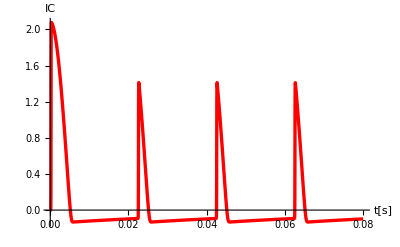
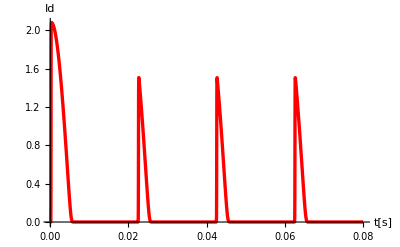
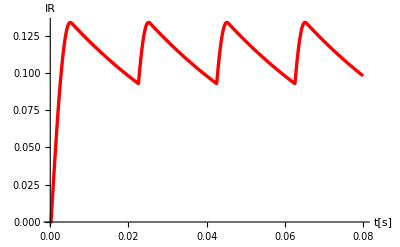
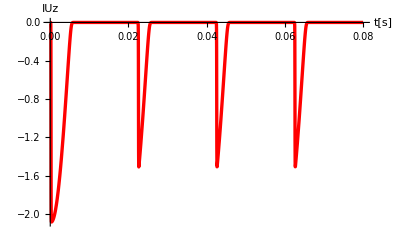
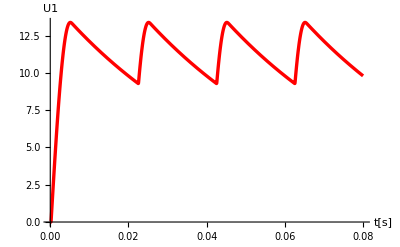
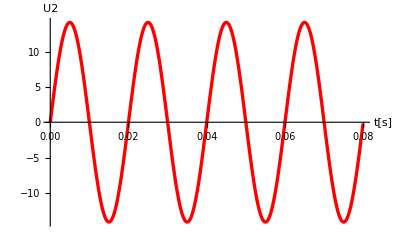

```mathematica
Plot[#[t] /. Res, {t, 0, tMax}, AxesLabel->{"t[s]", ToString[#]}, PlotRange->All, GridLines->Full, PlotStyle->{Red, Thickness[0.006]}] & /@ Nezname
```

## 6. Přednáška

### Parametrická řešení

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
R1 = 100;
R2 = 150;
R3 = 47;
R4 = 120;
R5 = 270;
Uz = 10;
Iz = 0.01;
```

```mathematica
Rovn = {0 == IUz + Iz +IR1,
Iz + IR1 == IR2 + IR3 + IR4,
IR3 + IR4  == IR5 + IOut,
U1 - U2 == R1 * IR1,
U2 == R2 * IR2,
U2 - U3 == R3 * IR3,
U2 - U3 == R4 * IR4,
U3 == R5 * IR5,
Uz == -U1
}
```

{0==0.01+IR1+IUz,0.01+IR1==IR2+IR3+IR4,IR3+IR4==IOut+IR5,U1-U2==100 IR1,U2==150 IR2,U2-U3==47 IR3,U2-U3==120 IR4,U3==270 IR5,10==-U1}

```mathematica
Nezname = Union[Cases[Rovn, _Symbol, {0, ∞}]]
Nezname = DeleteCases[Union[Cases[Rovn, _Symbol, {0, ∞}]], IOut]
Length /@ {Rovn, Nezname}
```

{IOut,IR1,IR2,IR3,IR4,IR5,IUz,U1,U2,U3}

{IR1,IR2,IR3,IR4,IR5,IUz,U1,U2,U3}

{9,9}

```mathematica
Res = Solve[Rovn, Nezname][[1]]
```

{IR1→-0.0549067+0.445333 IOut,IR2→-0.0300622-0.296889 IOut,IR3→-0.0106667+0.533333 IOut,IR4→-0.00417778+0.208889 IOut,IR5→-0.0148444-0.257778 IOut,IUz→0.0449067-0.445333 IOut,U1→-10.,U2→-4.50933-44.5333 IOut,U3→-4.008-69.6 IOut}

```mathematica
{Res[[9]], Ui = Res[[9,2,1]], Ri = Res[[9, 2, 2, 1]]}
```

{U3→-4.008-69.6 IOut,-4.008,-69.6}

### Řazení součástek a funkce Par a Ser

```mathematica
Quiet[Remove["Global`*"]];
```

Sériové řazení

```mathematica
Rovn = {IR1 == IR2,
UIn - UOut == R1 * IR1,
UOut == R2 * IR2}
Solve[Rovn, {UOut, IR1, IR2}][[1]]
```

{IR1==IR2,UIn-UOut==IR1 R1,UOut==IR2 R2}

{UOut→(R2 UIn)/(R1+R2),IR1→UIn/(R1+R2),IR2→UIn/(R1+R2)}

```mathematica
Quiet[Remove["Global`*"]];
```

Paralelní řazení

```mathematica
Rovn = {Iz == IR1 + IR2,
UR == R1 * IR1,
UR == R2 * IR2}
Solve[Rovn, {Iz, IR1, IR2}][[1]]
```

{Iz==IR1+IR2,UR==IR1 R1,UR==IR2 R2}

{Iz→((R1+R2) UR)/(R1 R2),IR1→UR/R1,IR2→UR/R2}

Funkce

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
Par[OdporPar_] := Total[OdporPar^-1]^-1
Par[{R1, R2, R3, R4}]
```

1880/87

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
Ser[OdporSer_] := Total[OdporSer]
Ser[{R1, R2, R3, R4}]
```

417

### Metoda zjednodušování

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
R1 = 100;
R2 = 150;
R3 = 47;
R4 = 120;
R5 = 270;
```

```mathematica
Par[OdporPar_] := Total[OdporPar^-1]^-1
Ser[OdporSer_] := Total[OdporSer]
```

```mathematica
RA = Ser[{R3, R4}];
RB = Par[{RA, R2}];
RC = Ser[{RB, R5}];
RD = Par[{RC, R1}]
N[RD]
```

553200/7117

77.7294

### Operační zesilovače

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
Rovn = {IR1 == IR2,
U1 == IR2 * R2,
UOut - U1 == R1 * IR2,
UOut == A * (UIn - U1)
};
Res = Solve[Rovn, {IR1, IR2, U1, UOut}][[1]] // Simplify
uout = UOut /. Res
uoutIdeal = Limit[uout, A -> ∞]
```

{IR1→(A UIn)/(R1+R2+A R2),IR2→(A UIn)/(R1+R2+A R2),U1→(A R2 UIn)/(R1+R2+A R2),UOut→(A (R1+R2) UIn)/(R1+R2+A R2)}

(A (R1+R2) UIn)/(R1+R2+A R2)

(R1 UIn+R2 UIn)/R2

## 7. Přednáška

### Operační zesilovač

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
Rovn = {IR1 == IR3,
IR2 == IR4,
uPlus == R4 * IR4,
U1 - uPlus == R2 * IR2,
U2 - uMinus == R1 * IR1,
uMinus - uOut == R3 * IR3,
uOut == A * (uPlus - uMinus)}

Neznam = {IR1, IR2, IR3, IR4, uPlus, uMinus, uOut};
Symb = Union[Cases[Rovn, _Symbol, {0, ∞}]]
Length /@ {Rovn, Neznam, Symb}

Res = Solve[Rovn, Neznam][[1]]
uout = Simplify[Limit[uOut /. Res, A -> ∞] /. {R1 -> R, R2 -> R, R3 -> Au * R, R4 -> Au * R}]
```

{IR1==IR3,IR2==IR4,uPlus==IR4 R4,U1-uPlus==IR2 R2,U2-uMinus==IR1 R1,uMinus-uOut==IR3 R3,uOut==A (-uMinus+uPlus)}

{A,IR1,IR2,IR3,IR4,R1,R2,R3,R4,U1,U2,uMinus,uOut,uPlus}

{7,7,14}

{IR1→-(A R4 U1-R2 U2-A R2 U2-R4 U2-A R4 U2)/((R1+A R1+R3) (R2+R4)),IR2→U1/(R2+R4),IR3→-(A R4 U1-R2 U2-A R2 U2-R4 U2-A R4 U2)/((R1+A R1+R3) (R2+R4)),IR4→U1/(R2+R4),uPlus→(R4 U1)/(R2+R4),uMinus→-(-A R1 R4 U1-R2 R3 U2-R3 R4 U2)/((R1+A R1+R3) (R2+R4)),uOut→-((-A R1 R4 U1-A R3 R4 U1+A R2 R3 U2+A R3 R4 U2)/((R1+A R1+R3) (R2+R4)))}

Au (U1-U2)

```mathematica
Simplify[Limit[-U1/IR1 /. Res, A -> ∞] //. {R1 -> R, R2 -> R, R3 -> Au * R, R4 -> Au * R}] /. U2 -> 0
```

((1+Au) R)/Au

### Harmonický ustálený stav

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
n = 1;
Rovn = 0 == ∑_(i=0)^n Subscript[a, 1]*x^i
Solve[Rovn, x]
```

0==a_1+x a_1

{{x→-1}}

```mathematica
n = 2;
Rovn = 0 == ∑_(i=0)^n Subscript[a, 1]*x^i
Solve[Rovn, x]
```

0==a_1+x a_1+x^2 a_1

{{x→-(-1)^(1/3)},{x→(-1)^(2/3)}}

```mathematica
n = 3;
Rovn = 0 == ∑_(i=0)^n Subscript[a, 1]*x^i
Solve[Rovn, x]
```

0==a_1+x a_1+x^2 a_1+x^3 a_1

{{x→-1},{x→-ⅈ},{x→ⅈ}}

### Obvod HUS

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
UIn = 10 * Sin[314 t];
L = 0.033;
μF = 10^-6;
Cl = 4.7 μF;
R1 = 47;
R2 = 100;
```

{IL[t]+IR1[t]==ICl[t]+IR2[t],UOut[t]==100 IR2[t],ICl[t]==4.7×10^-6 UOut'[t],10 Sin[314 t]-UOut[t]==47 IR1[t],10 Sin[314 t]-UOut[t]==0.033 IL'[t]}

{ICl,IL,IR1,IR2,UOut}

{5,5}

{IL[0]==0,UOut[0]==0}

{ICl[t]==4.7×10^-6 UOut'[t],IL[0]==0,IL[t]+IR1[t]==ICl[t]+IR2[t],UOut[0]==0,10 Sin[314 t]-UOut[t]==47 IR1[t],10 Sin[314 t]-UOut[t]==0.033 IL'[t],UOut[t]==100 IR2[t]}

{ICl→InterpolatingFunction[…],IL→InterpolatingFunction[…],IR1→InterpolatingFunction[…],IR2→InterpolatingFunction[…],UOut→InterpolatingFunction[…]}

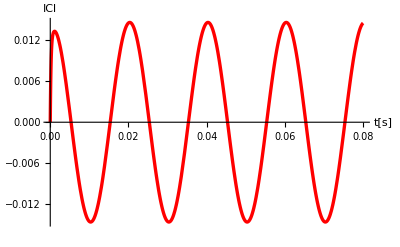
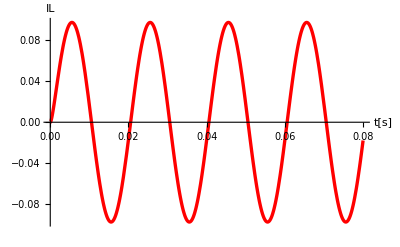
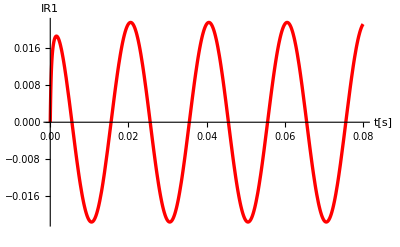
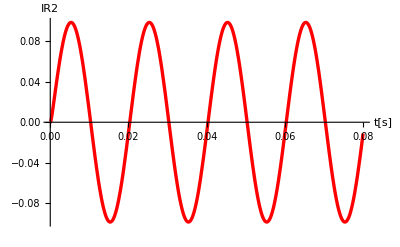
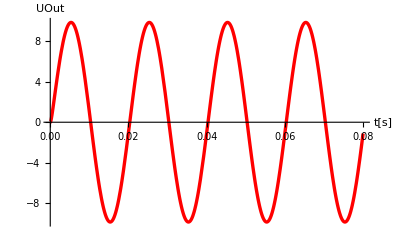

```mathematica
Rovn = {IR1[t] + IL[t] == ICl[t] + IR2[t],
UOut[t] == R2 * IR2[t],
ICl[t] == Cl * UOut'[t],
UIn - UOut[t] == R1 * IR1[t],
UIn - UOut[t] == L * IL'[t]
}
Nezname = Union[Cases[Rovn, a_Symbol[t] :> a, {0, ∞}]]
Length /@ {Rovn, Nezname}
PocPod = Union[Cases[Rovn, a_'[t] :> a[0] == 0, {0, ∞}]]
RovnPod = Union[Rovn, PocPod]
tMax = 0.08;
Res = NDSolve[RovnPod, Nezname, {t, 0, tMax}, StartingStepSize->10^-9][[1]]
Plot[#[t] /. Res, {t, 0, tMax}, AxesLabel->{"t[s]", ToString[#]}, PlotRange->All, GridLines->Full, PlotStyle->{Red, Thickness[0.006]}] & /@ Nezname
```

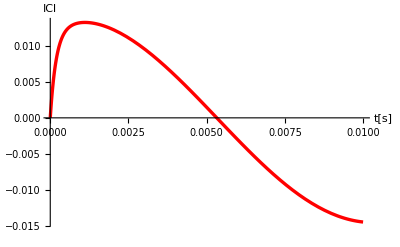
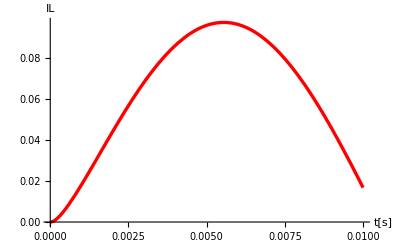
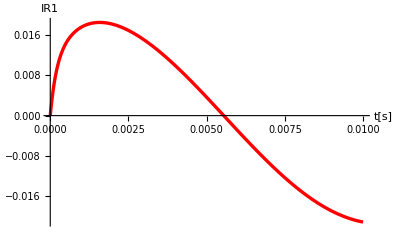
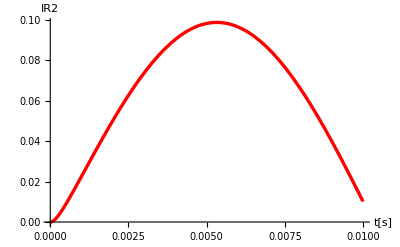
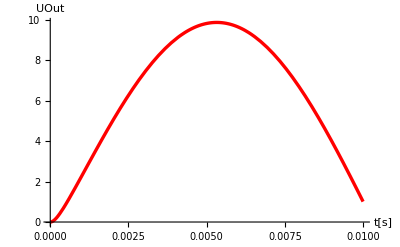

```mathematica
tMax = 0.01;
Res = NDSolve[RovnPod, Nezname, {t, 0, tMax}, StartingStepSize->10^-9][[1]];
Plot[#[t] /. Res, {t, 0, tMax}, AxesLabel->{"t[s]", ToString[#]}, PlotRange->All, GridLines->Full, PlotStyle->{Red, Thickness[0.006]}] & /@ Nezname
```

```mathematica
FullForm[ICl /. Res]
```

### Matematika HUS

```mathematica
Quiet[Remove["Global`*"]];
```

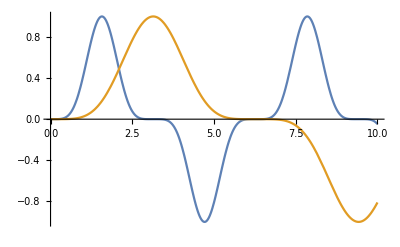

```mathematica
g[t_] := Sin[t]^5;
T1 = 2 Pi;
T2 = 2*2Pi;
h[t_] := g[T1/T2*t];
Plot[{g[t], h[t]}, {t, 0, 10}]
```

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
Sin[ω * t]^3 // TrigReduce
```

1/4 (3 Sin[t ω]-Sin[3 t ω])

```mathematica
2*Sin[3t + 0.2] + 0.5*Sin[3t - 0.4]
```

-0.5 Sin[0.4-3 t]+2 Sin[0.2+3 t]

```mathematica
Series[Sin[x], {x, 0, 5}]
```

x-x^3/6+x^5/120+O[x]^6

### Fázory

```mathematica
Quiet[Remove["Global`*"]];
```

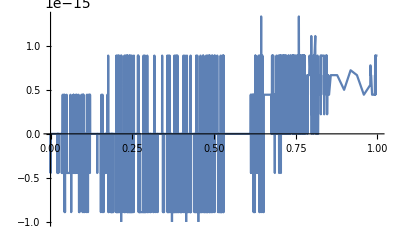

```mathematica
U1[t_] := 5*Sin[3t + 0.4]
U2[t_] := Im[5 * Exp[I * 0.4] * Exp[I * 3 * t]]
Plot[U1[t] - U2[t], {t, 0, 1}]
```

## 8. Přednáška

### Komplexní čísla

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
z = 3 + 4I
```

3+4 ⅈ

```mathematica
?I
```

```mathematica
{z, Re[z], Im[z], Abs[z], √(Re[z]^2+ Im[z]^2), Arg[z]}
```

{3+4 ⅈ,3,4,5,5,ArcTan[4/3]}

```mathematica
Arg /@ {0, I, -1, -I}
```

{0,π/2,π,-π/2}

```mathematica
?Arg
```

```mathematica
U1[t_] := 5*Sin[3t + 0.4]
U2[t_] := Im[5 * Exp[I * 0.4] * Exp[I * 3 * t]]
Plot[U1[t] - U2[t], {t, 0, 1}]
```

-Graphics-

```mathematica
Sin[psi + Pi/2]
```

Cos[psi]

```mathematica
Sin'
```

Cos[#1]&

```mathematica
{Abs[I], Arg[I]}
```

{1,π/2}

### Chování RLC v HUS

R: u_R(t) = R*I_R(t) 
	U_R = R*I_R
L: u_L(t) = L*dI_L/dt
	U_L = L*j*ω*I
C: I_c(t) = C*dU_c/dt
	I_C = C*j*ω*U_C
U_C = 1/(j*ω*C)*I_C

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
L = 33 mH;
mH = 10^-3;
IL[t_] := 10^-3*Sin[1000t +0.123]
UL[t_] := L * IL'[t]
```

```mathematica
ILFaz = 0.001 * E^(I*0.123);
Print["ILFazor = ", ILFaz, " A"]
```

ILFazor = 0.000992445+0.00012269 ⅈ A

```mathematica
ω = 1000;
ULFaz = I * ω * L * ILFaz;
Print["ULFazor = ", ULFaz, " V"]
```

ULFazor = -0.00404877+0.0327507 ⅈ V

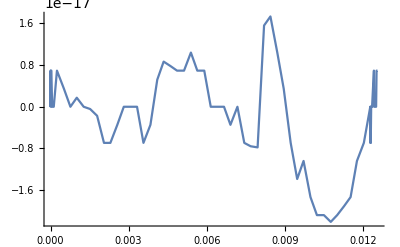

```mathematica
ULtFaz[t_] := Im[ULFaz * E^(I*ω*t)] 
T = (2Pi)/ω;
Plot[UL[t] - ULtFaz[t], {t,0,2T}]
```

```mathematica
{Arg[ILFaz], Arg[ULFaz]}
```

{0.123,1.6938}

```mathematica
(Arg[ILFaz] - Arg[ULFaz])/Pi
```

-0.5

### Vypočítaný obvod

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
L= 33 mH;
mH = 10^-3;
Cl = 4.7 υF;
υF = 10^-6;
R1 = 100;
R2 = 200;
Uz = 10*Sin[cos[t] + 0.123]
Um = 10.;
fi = 0.123;
ω = 1000;
T = (2Pi)/ω;
UzFaz = Um * E^(I*ω)
```

10 Sin[0.123+cos[t]]

5.62379+8.2688 ⅈ

```mathematica
Rovn = {
Iuz == IR1 + IC,
IR1 + IC == IR2 + IL,

U1 == R2 * IR2,
U1 ==  I * ω * L * IL,
UzFaz - U1 == R1 * IR1,
UzFaz - U1 == 1/(I * ω * Cl)* IC
}
```

{Iuz==IC+IR1,IC+IR1==IL+IR2,U1==200 IR2,U1==33 ⅈ IL,(5.62379+8.2688 ⅈ)-U1==100 IR1,(5.62379+8.2688 ⅈ)-U1==(0.-212.766 ⅈ) IC}

```mathematica
Neznam =Union[Cases[Rovn, _Symbol, {0, ∞}]]
```

{IC,IL,IR1,IR2,Iuz,U1}

```mathematica
Length /@ {Rovn, Neznam}
```

{6,6}

```mathematica
Res = Solve[Rovn][[1]]
```

{IC→-0.027752+0.0399534 ⅈ,IL→0.0716398+0.0871796 ⅈ,IR1→0.0850072+0.0590468 ⅈ,IR2→-0.0143846+0.0118206 ⅈ,Iuz→0.0572552+0.0990002 ⅈ,U1→-2.87693+2.36411 ⅈ}

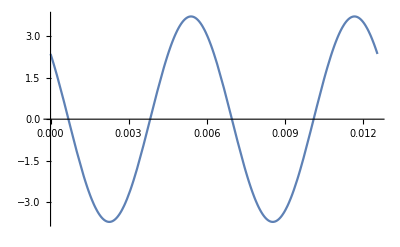

```mathematica
U1[t_] := Im[(U1 /. Res) * E^(I*ω*t)]
Plot[U1[t], {t, 0, 2T}]
```

```mathematica
U1 /. Res
Print["Amplituda U1 = ", Abs[U1 /. Res], " V"]
Print["Počáteční fáze U1 = ", Arg[U1 /. Res], " Rad"]
```

-2.87693+2.36411 ⅈ

Amplituda U1 = 3.72367 V

Počáteční fáze U1 = 2.45373 Rad

### Zvuk

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
Play[Sin[440 * 2Pi t], {t, 0, 1}]
```

-Graphics-

```mathematica
Play[{Sin[440 * 2Pi t], Sin[360 * 2Pi t]}, {t, 0, 1}]
```

-Graphics-

## 9. Přednáška

### Funkce Ser a Par pro RLC

```mathematica
Quiet[Remove["Global`*"]];
```

U_R = R * I_R     => Z_R = R
U_L = jωL * I_L     => Z_L = jωL
U_C = 1/JωC* I_C     => Z_C = 1/jωC

```mathematica
Ser[OdporSer_]:=Total[OdporSer]
Ser[{R1,R2,R3,R4}]
```

R1+R2+R3+R4

```mathematica
Par[OdporPar_]:=Total[OdporPar^-1]^-1
Par[{R1,R2,R3,R4}]
```

1/(1/R1+1/R2+1/R3+1/R4)

```mathematica
L= 33 mH;
mH = 10^-3;
Cl = 4.7 υF;
υF = 10^-6;
R1 = 100;
R2 = 200;
Uz = 10*Sin[cos[t] + 0.123]
Um = 10.;
fi = 0.123;
ω = 1000;
T = (2Pi)/ω;
UzFaz = Um * E^(I*ω)
```

10 Sin[0.123+cos[t]]

5.62379+8.2688 ⅈ

```mathematica
Rovn = {
Iuz == IR1 + IC,
IR1 + IC == IR2 + IL,

U1 == R2 * IR2,
U1 ==  I * ω * L * IL,
UzFaz - U1 == R1 * IR1,
UzFaz - U1 == 1/(I * ω * Cl)* IC
}
```

{Iuz==IC+IR1,IC+IR1==IL+IR2,U1==200 IR2,U1==33 ⅈ IL,(5.62379+8.2688 ⅈ)-U1==100 IR1,(5.62379+8.2688 ⅈ)-U1==(0.-212.766 ⅈ) IC}

```mathematica
Neznam =Union[Cases[Rovn, _Symbol, {0, ∞}]];
Length /@ {Rovn, Neznam};
Res = Solve[Rovn][[1]];
```

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
Ser[OdporSer_]:=Total[OdporSer]
Par[OdporPar_]:=Total[OdporPar^-1]^-1
Z1 = Par[{R1, 1/(I * ω * Cl)}]
Z2 = Par[{R2, I * ω * L}]
```

1/(1/R1+ⅈ Cl ω)

1/(1/R2-ⅈ/(L ω))

```mathematica
IUZDel = UzFaz/Ser[{Z1, Z2}]
Iuz /. Res
```

UzFaz/Ser[{1/(1/R1+ⅈ Cl ω),1/(1/R2-ⅈ/(L ω))}]

ReplaceAll::reps: {Res} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Iuz/.Res

```mathematica
U1Del = UzFaz * Z2/(Z1 + Z2)  //Simplify
U1Del /. ω -> 0
Limit[U1Del, ω -> ∞]
```

(L R2 UzFaz ω (-ⅈ+Cl R1 ω))/(-ⅈ L R1 ω-ⅈ L R2 ω+R1 R2 (-1+Cl L ω^2))

0

UzFaz

```mathematica
?Chop
```

### Přenosná funkce

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
L= 33 mH;
mH = 10^-3;
Cl = 4.7 υF;
υF = 10^-6;
R1 = 100;
R2 = 200;
Uz = 10*Sin[cos[t] + 0.123]
Um = 10.;
fi = 0.123;
ω = 1000;
T = (2Pi)/ω;
UzFaz = Um * E^(I*ω)
```

10 Sin[0.123+cos[t]]

5.62379+8.2688 ⅈ

```mathematica
Ser[OdporSer_]:=Total[OdporSer]
Par[OdporPar_]:=Total[OdporPar^-1]^-1
Z1 = Par[{R1, 1/(I * ω * Cl)}]
Z2 = Par[{R2, I * ω * L}]
```

1/(1/R1+ⅈ Cl ω)

1/(1/R2-ⅈ/(L ω))

```mathematica
IUZDel = UzFaz/Ser[{Z1, Z2}]
U1Del = UzFaz * Z2/(Z1 + Z2)  //Simplify
```

UzFaz/(1/(1/R2-ⅈ/(L ω))+1/(1/R1+ⅈ Cl ω))

(L R2 UzFaz ω (-ⅈ+Cl R1 ω))/(-ⅈ L R1 ω-ⅈ L R2 ω+R1 R2 (-1+Cl L ω^2))

```mathematica
Prenos = U1Del/UzFaz //Simplify
```

(L R2 ω (-ⅈ+Cl R1 ω))/(-ⅈ L R1 ω-ⅈ L R2 ω+R1 R2 (-1+Cl L ω^2))

```mathematica
L= 33 mH;
mH = 10^-3;
Cl = 4.7 υF;
υF = 10^-6;
R1 = 100;
R2 = 200;
```

```mathematica
Prenos = U1Del/UzFaz //Simplify
```

(1. ω ((0.-2127.66 ⅈ)+1. ω))/(-6.44745×10^6-(0.+3191.49 ⅈ) ω+1. ω^2)

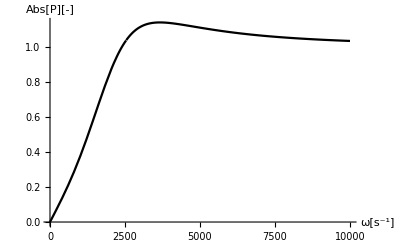

```mathematica
Plot[Abs[Prenos], {ω, 0.1, 10^4}, PlotStyle->Black, AxesLabel->{"ω[s^-1]", "Abs[P][-]"}, GridLines->Full, PlotRange->All]
```

### Řešení obvodu

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
Ser[OdporSer_]:=Total[OdporSer]
Par[OdporPar_]:=Total[OdporPar^-1]^-1
Z1 = Ser[{R1, I * ω * L1, 1/(I * ω * C1)}];
Z2 = Par[{Ser[{R2, I * ω * L2}], 1/(I * ω * C2)}];
Prenos = Z2/(Z1 + Z1);
```

```mathematica
R1 = 1;
R2 = 1;
L1 = 10^-3;
L2 = 10^-6;
C1 = 10^-6;
C2 = 10^-9;
```

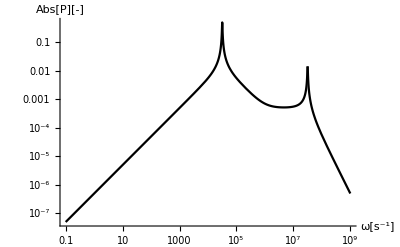

```mathematica
LogLogPlot[Abs[Prenos], {ω, 0.1, 10^9}, PlotStyle->Black, AxesLabel->{"ω[s^-1]", "Abs[P][-]"}, GridLines->Full, PlotRange->All]
```

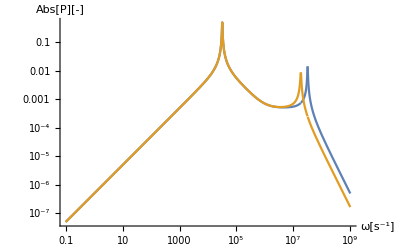

```mathematica
Clear[C2];
LogLogPlot[Evaluate[Abs[Prenos] /. {{C2 -> 10^-9}, {C2 -> 3*10^-9}}], {ω, 0.1, 10^9}, AxesLabel->{"ω[s^-1]", "Abs[P][-]"}, GridLines->Full, PlotRange->All]
```

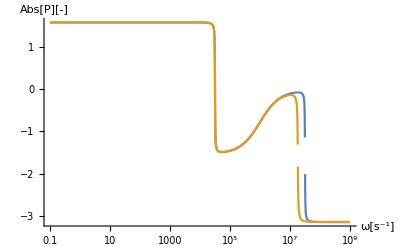

```mathematica
LogLinearPlot[Evaluate[Arg[Prenos] /. {{C2 -> 10^-9}, {C2 -> 3*10^-9}}], {ω, 0.1, 10^9}, AxesLabel->{"ω[s^-1]", "Abs[P][-]"}, GridLines->Full, PlotRange->All]
```

### Hledání funkcí

```mathematica
?*Plot*
```

### Fourierovy řady

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
n = 10;
Vyraz = ∑_(i=0)^n (Subscript[a, i]*Cos[i *(2Pi)/T* t] + Subscript[b, i]*Sin[i *(2Pi)/T * t])
```

a_0+Cos[(2 π t)/T] a_1+Cos[(4 π t)/T] a_2+Cos[(6 π t)/T] a_3+Cos[(8 π t)/T] a_4+Cos[(10 π t)/T] a_5+Cos[(12 π t)/T] a_6+Cos[(14 π t)/T] a_7+Cos[(16 π t)/T] a_8+Cos[(18 π t)/T] a_9+Cos[(20 π t)/T] a_10+Sin[(2 π t)/T] b_1+Sin[(4 π t)/T] b_2+Sin[(6 π t)/T] b_3+Sin[(8 π t)/T] b_4+Sin[(10 π t)/T] b_5+Sin[(12 π t)/T] b_6+Sin[(14 π t)/T] b_7+Sin[(16 π t)/T] b_8+Sin[(18 π t)/T] b_9+Sin[(20 π t)/T] b_10

```mathematica
Integrate[Vyraz, {t, t1, t1 + T}]
```

T a_0

```mathematica
Integrate[Vyraz * Sin[2 * (2Pi * t)/T], {t, t1, t1 + T}]
Integrate[Vyraz * Cos[2 * (2Pi * t)/T], {t, t1, t1 + T}]
```

(T b_2)/2

(T a_2)/2

```mathematica
Quiet[Remove["Global`*"]];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

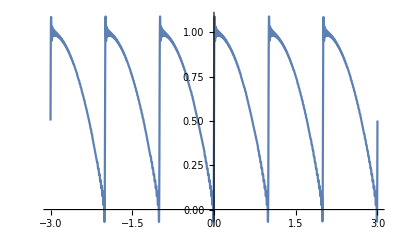

```mathematica
f[t_] := 1 - t^2;
T = 1;
a[0] := 1/T * NIntegrate[f[t], {t, 0 ,T}]
a[i_Integer] := 2/T * NIntegrate[f[t] * Cos[i * (2Pi * t)/T], {t, 0, T}]
b[i_Integer] := 2/T * NIntegrate[f[t] * Sin[i * (2Pi * t)/T], {t, 0, T}]
Vyraz = Sum[a[i]*Cos[i *(2Pi)/T* t] + b[i]*Sin[i *(2Pi)/T * t], {i, 0, 50}];
Plot[f[t], {t, 0, 1}];
Plot[Vyraz, {t, -3, 3}]
```

```mathematica
?Quiet
```

## 10. Přednáška

### Rozvoj periodické funkce

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
Vyraz = Sum[a[i]*Cos[i *(2Pi)/T* t] + b[i]*Sin[i *(2Pi)/T * t], {i, 0, 5}]
Integrate[Vyraz , {t, t1, t1 + T}]
Integrate[{Vyraz * Cos[(2Pi * t)/T], Vyraz * Sin[(2Pi * t)/T]}, {t, t1, t1 + T}]
```

a[0]+a[1] Cos[(2 π t)/T]+a[2] Cos[(4 π t)/T]+a[3] Cos[(6 π t)/T]+a[4] Cos[(8 π t)/T]+a[5] Cos[(10 π t)/T]+b[1] Sin[(2 π t)/T]+b[2] Sin[(4 π t)/T]+b[3] Sin[(6 π t)/T]+b[4] Sin[(8 π t)/T]+b[5] Sin[(10 π t)/T]

T a[0]

{1/2 T a[1],1/2 T b[1]}